```mathematica
SetDirectory[NotebookDirectory[]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"utility_generator_functions.nb"}]]
```

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа

BooleanRegion[#1||#2&,{Polygon[…],Polygon[…]}]

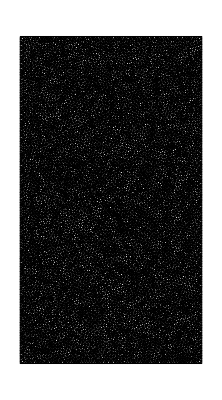

```mathematica
configPath="D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\";
Mcm=50;
(*TO DO: Fix the borders and source and MCM*)
left=0;
right=500;
lower=0;
middle=600;
upper=900;
region=Rectangle[{left,lower},{right,upper}];
polygonVertices1={{150,900},{147,800},{130,900}};
cavity1=Polygon[polygonVertices1];
polygonVertices2={{250,900},{237,800},{230,900}};
cavity2=Polygon[polygonVertices2];
cavity=RegionUnion[cavity1, cavity2]
(*900m, 850m, 700m, 600m, 10m*)
(*повече от 1 пукнатина*)
(*2 събития- без и с 1 пукнатина, 1 повърхностно и едно земетресение, 2 повърхностни събития*)

(*Create region with cavity- for display, config file and air meshing, do not use it for water*)
regionWithCavity=RegionDifference[region,cavity1];
regionWithCavity=RegionDifference[regionWithCavity,cavity2];
Needs["NDSolve`FEM`"];
(*em=ToElementMesh[region,"MeshOrder"->1];*)
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement","MeshQualityGoal"->0.9,MaxCellMeasure->Mcm];
Show[em["Wireframe"]]
elements=em["MeshElements"][[1,1]];
nodes = em["Coordinates"];
elementsLen=Length[elements];
```

```mathematica
nodes[[elements[[2864]]]]
```

{{171.174,21.899},{175.449,24.6732},{171.244,29.2635}}

```mathematica
(*Check if mesh is ok*)
t = Table[{nodes[[i]],1},{i,1,Length[nodes]}];
(*Print["table: ",table];*)
intF = Interpolation[t,InterpolationOrder->1];
```

```mathematica
Length[elements]
Length[nodes]
getLongestEdgeInMesh[nodes,elements]
minLen
```

14248

7324

14.7899

6.2083

```mathematica
nodes[[elements[[1603]]]]
nodes[[139]]
```

{{293.592,719.256},{317.436,706.718},{318.143,722.87}}

{16.25,900.}

```mathematica
nodes[[elements[[23672]]]]
```

{{310.144,699.326},{304.207,697.924},{307.735,692.082}}

```mathematica
setUpMeshForCpp[nodes,elements]
```

Exported nodes and elements

Found source

Resolved seismograh points

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[List,=].

sourceElement

seismographIndices

mcm

tau

depths

left

right

cavityIndices

```mathematica
(*Честотен анализ на сеизмограма*)
matrixFreqAnalysis=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_25.csv"];Dimensions[matrixFreqAnalysis]
```

{10003,4}

Analyzing 10Hz main frequency

251

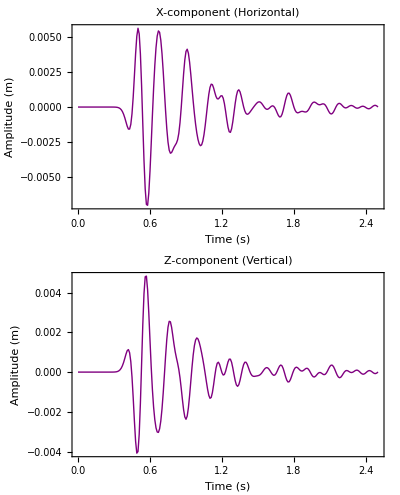

```mathematica
Print["Analyzing 10Hz main frequency"]
dt=0.00025;(*time step in seconds,adjust this*)time=Range[0,(Length[matrixFreqAnalysis[[1;;-1,1]]]-1)*dt,40*dt];
seismoX=Table[matrixFreqAnalysis[[i,1]],{i,1,Length[matrixFreqAnalysis],40}];
seismoZ=Table[matrixFreqAnalysis[[i,2]],{i,1,Length[matrixFreqAnalysis],40}];
Length[seismoX]
(*Plot with time-labeled x-axis*)
xPlot=ListLinePlot[Transpose[{time,seismoX}],Frame->True,
PlotLabel->"X-component (Horizontal)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Purple},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All];
zPlot=ListLinePlot[Transpose[{time,seismoZ}],Frame->True,
PlotLabel->"Z-component (Vertical)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Purple},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All];
combined=GraphicsGrid[{{xPlot},{zPlot}},Spacings->{0.5,1}]
```

0.000249925

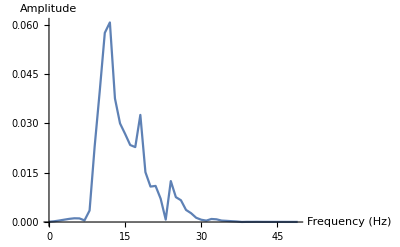

```mathematica
T=2.5;
dT=T/Length[matrixFreqAnalysis[[1;;-1,1]]]
fs=T/dT;
fftX=Fourier[matrixFreqAnalysis[[1;;-1,1]]];
n=Length[matrixFreqAnalysis[[1;;-1,1]]];
freqs=fs*Range[0,n-1]/n;
half=Floor[n/200];
freqsHalf=freqs[[1;;half]];
fftHalf=Abs[fftX[[1;;half]]];
ListLinePlot[Transpose[{freqsHalf,fftHalf}],AxesLabel->{"Frequency (Hz)","Amplitude"},PlotRange->All]
```

{1002,2}

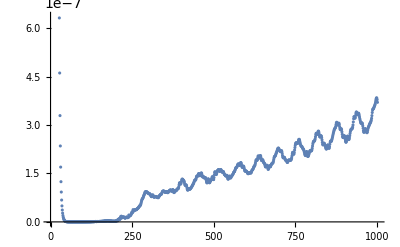

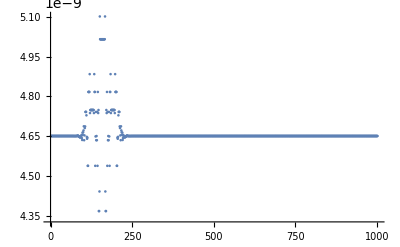

```mathematica
(*Тестване за стабилност на решението поради голямо число на обусловеност*)
matrixErrors=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\errors"];
Dimensions[matrixErrors]
dt=0.0025;(*time step in seconds,adjust this*)time=Range[0,(Length[matrixErrors[[1;;-1,1]]]-1)*dt,40*dt];
err=Table[matrixErrors[[i,1]],{i,1,Length[matrixErrors],40}];
Length[err]
(*Plot with time-labeled x-axis*)
xPlot=ListLinePlot[Transpose[{time,err}],Frame->True,
PlotLabel->"X-component (Horizontal)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Gray},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All];
ListPlot[matrixErrors[[1;;-1,1]]]
ListPlot[matrixErrors[[1;;-1,2]]]
```

```mathematica
(*Refinements and practical error meaurement*)
matrixRefinement1=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_200CFLFinsl.csv"];
Dimensions[matrixRefinement1]
```

{5,7364}

```mathematica
xy1= Table[matrixRefinement1[[1;;5,Length[matrixRefinement1[[1]]]/2 + i]],{i,1,2*Length[nodes]}];
Dimensions[xy1]
```

{3682,5}

```mathematica
norm1=Table[{nodes[[i]],Sqrt[xy1[[2*i-1,t]]^2+xy1[[2*i,t]]^2]},{t,1,5},{i,1,Length[nodes]}];
Dimensions[norm1]
```

{5,1841,2}

```mathematica
ihat1=Table[Interpolation[norm1[[j]],InterpolationOrder->1],{j,1,5}];
```

```mathematica
Plot3D[ihat1[[5]][x,y],{x,y}∈regionWithCavity,PlotRange->All]
```

-Graphics3D-

```mathematica
nodes[[139]]
```

{16.25,900.}

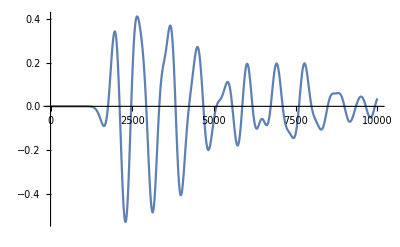

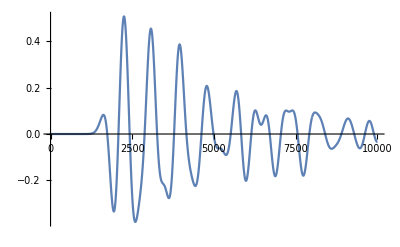

```mathematica
seismoRefinement1=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_200Refine1.csv"];
ListLinePlot[seismoRefinement1[[1;;-1,1]]]
ListLinePlot[seismoRefinement1[[1;;-1,2]]]
```

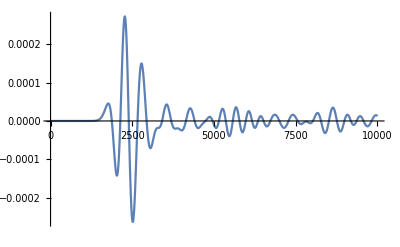

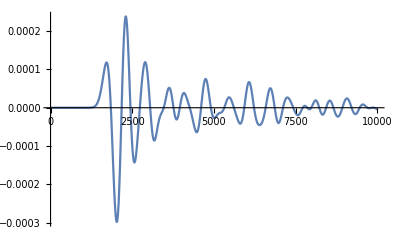

```mathematica
seismoRefinement2=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_50Refine1.csv"];
ListLinePlot[seismoRefinement2[[1;;-1,1]],PlotRange->All]
ListLinePlot[seismoRefinement2[[1;;-1,2]],PlotRange->All]
```

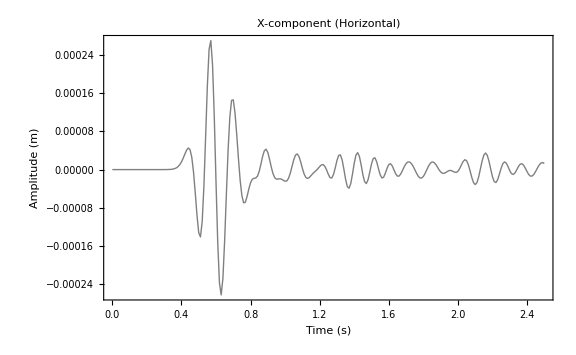

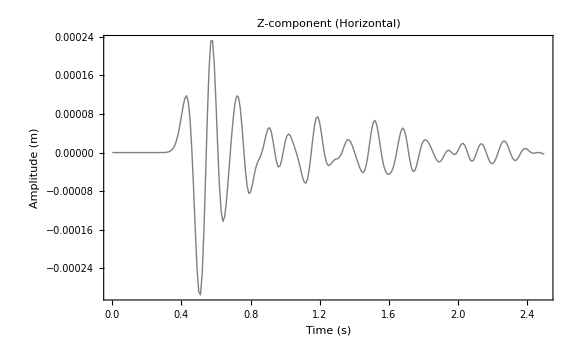

```mathematica
dt=0.00025;
time=Range[0,(Length[seismoRefinement2[[1;;-1,1]]]-1)*dt,40*dt];
seismoX=Table[seismoRefinement2[[i,1]],{i,1,Length[seismoRefinement2],40}];xPlot=ListLinePlot[Transpose[{time,seismoX}],Frame->True,
PlotLabel->"X-component (Horizontal)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Gray},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]

seismoY=Table[seismoRefinement2[[i,2]],{i,1,Length[seismoRefinement2],40}];
yPlot=ListLinePlot[Transpose[{time,seismoY}],Frame->True,
PlotLabel->"Z-component (Horizontal)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Gray},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All]
```

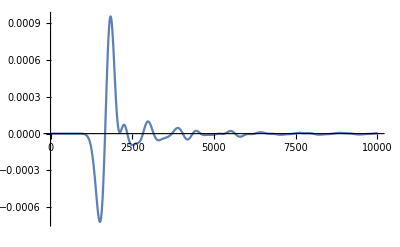

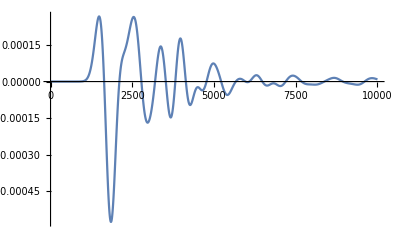

```mathematica
seismoRefinement3=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_12.5Refine1.csv"];
ListLinePlot[seismoRefinement3[[1;;-1,1]],PlotRange->All]
ListLinePlot[seismoRefinement3[[1;;-1,2]],PlotRange->All]
```

```mathematica
Dimensions[seismoRefinement1]
```

{10003,4}

```mathematica
matrixRefinement2=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_50CFLFinsl.csv"];
Dimensions[matrixRefinement2]
```

{5,28800}

```mathematica
xy2= Table[matrixRefinement2[[1;;5,Length[matrixRefinement2[[1]]]/2 + i]],{i,1,2*Length[nodes]}];
```

```mathematica
norm2=Table[{nodes[[i]],Sqrt[xy2[[2*i-1,t]]^2+xy2[[2*i,t]]^2]},{t,1,5},{i,1,Length[nodes]}];
Dimensions[norm2]
```

{5,1841,2}

```mathematica
ihat2=Table[Interpolation[norm2[[j]],InterpolationOrder->1],{j,1,5}];
```

```mathematica
Plot3D[ihat2[[5]][x,y],{x,y}∈regionWithCavity,PlotRange->All]
```

-Graphics3D-

```mathematica
matrixRefinement3=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_12.5CFLFinsl.csv"];
Dimensions[matrixRefinement3]
```

{5,113900}

```mathematica
xy3= Table[matrixRefinement3[[1;;5,Length[matrixRefinement3[[1]]]/2 + i]],{i,1,2*Length[nodes]}];
```

```mathematica
norm3=Table[{nodes[[i]],Sqrt[xy3[[2*i-1,t]]^2+xy3[[2*i,t]]^2]},{t,1,5},{i,1,Length[nodes]}];
Dimensions[norm3]
```

{5,1841,2}

```mathematica
ihat3=Table[Interpolation[norm3[[j]],InterpolationOrder->1],{j,1,5}];
```

```mathematica
Plot3D[ihat3[[5]][x,y],{x,y}∈regionWithCavity,PlotRange->All]
```

-Graphics3D-

```mathematica
diffCoarse = Norm[xy1-xy2];
diffFine=Norm[xy2-xy3];
p=Log[diffCoarse/diffFine]/Log[2]
```

1.89656

```mathematica
diffCoarse = Norm[xy1[[1;;-1,5]]-xy2[[1;;-1,5]]];
diffFine=Norm[xy2[[1;;-1,5]]-xy3[[1;;-1,5]]];
p=Log[diffCoarse/diffFine]/Log[2]
```

1.49161

{3682,5}

```mathematica
Norm[diff[[1;;-1,5]]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Norm[Symbol[]]

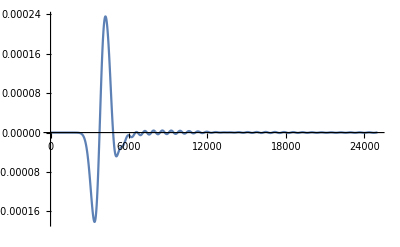

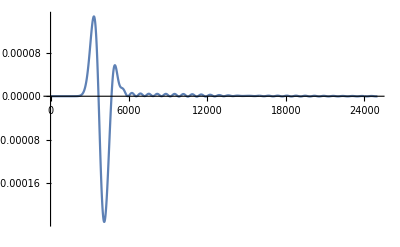

```mathematica
(*CFL Refinement*)
seismoRefinementCFL12=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_12.5RefineCFL.csv"];
ListLinePlot[seismoRefinementCFL12[[1;;-1,1]],PlotRange->All]
ListLinePlot[seismoRefinementCFL12[[1;;-1,2]],PlotRange->All]
```

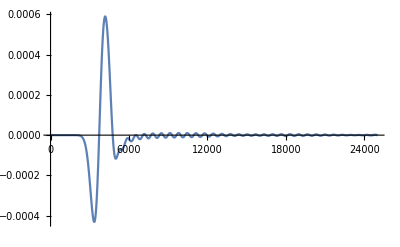

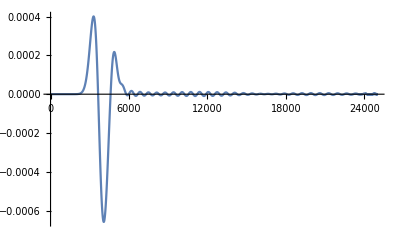

```mathematica
seismoRefinementCFL50=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_50RefineCFL.csv"];
ListLinePlot[seismoRefinementCFL50[[1;;-1,1]],PlotRange->All]
ListLinePlot[seismoRefinementCFL50[[1;;-1,2]],PlotRange->All]
```

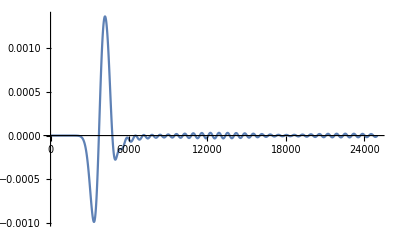

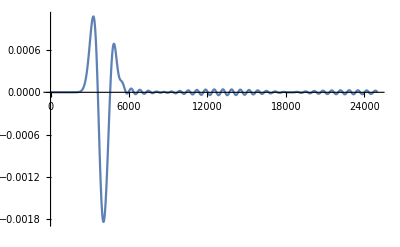

```mathematica
seismoRefinementCFL200=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_200RefineCFL.csv"];
ListLinePlot[seismoRefinementCFL200[[1;;-1,1]],PlotRange->All]
ListLinePlot[seismoRefinementCFL200[[1;;-1,2]],PlotRange->All]
```

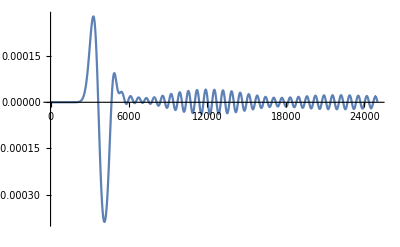

```mathematica
ListLinePlot[15/9*seismoRefinementCFL50[[1;;-1,1]]-seismoRefinementCFL200[[1;;-1,1]],PlotRange->All]
```

```mathematica
Log[Norm[seismoRefinementCFL200[[1;;-1,1]]-seismoRefinementCFL50[[1;;-1,1]]]/Norm[seismoRefinementCFL50[[1;;-1,1]]-seismoRefinementCFL12[[1;;-1,1]]]]/Log[2]
Log[Norm[seismoRefinementCFL200[[1;;-1,2]]-seismoRefinementCFL50[[1;;-1,2]]]/Norm[seismoRefinementCFL50[[1;;-1,2]]-seismoRefinementCFL12[[1;;-1,2]]]]/Log[2]
```

1.14913

1.46265

```mathematica
Dimensions[seismoRefinementCFL]
```

{25001,64}

```mathematica
matrixS250=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_25.csv"];Dimensions[matrixS250]
```

{16003,4}

1event_0cavities_300_10_source

401

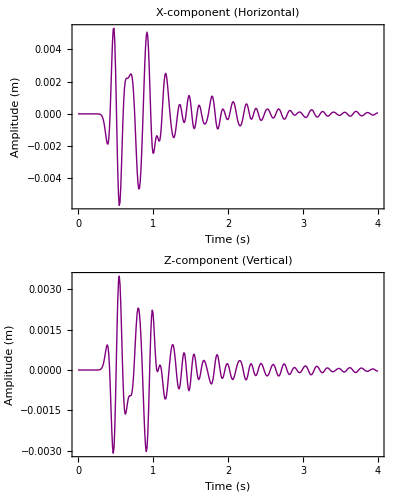

```mathematica
Print["1event_0cavities_300_10_source"]
dt=0.00025;(*time step in seconds,adjust this*)time=Range[0,(Length[matrixS250[[1;;-1,1]]]-1)*dt,40*dt];
seismoX=Table[matrixS250[[i,1]],{i,1,Length[matrixS250],40}];
seismoZ=Table[matrixS250[[i,2]],{i,1,Length[matrixS250],40}];
Length[seismo]
(*Plot with time-labeled x-axis*)
xPlot=ListLinePlot[Transpose[{time,seismoX}],Frame->True,
PlotLabel->"X-component (Horizontal)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Purple},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All];
zPlot=ListLinePlot[Transpose[{time,seismoZ}],Frame->True,
PlotLabel->"Z-component (Vertical)",
FrameLabel->{"Time (s)","Amplitude (m)"},PlotStyle->{Thick,Purple},LabelStyle->Directive[FontFamily->"Times",14],FrameTicks->{Automatic,Automatic},ImageSize->Large,PlotRange->All];
combined=GraphicsGrid[{{xPlot},{zPlot}},Spacings->{0.5,1}]
```

```mathematica
Export["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\seismogram results\\displacement_500x900_25_layer_0_600_900_10Hz_tau=0.00025\\2event_2water_cavity_300_(780_900)_source.pdf",combined];
```

```mathematica
minLen/Sqrt[3*(3535.53^2+7071^2)]
```

0.000321098

```mathematica
nodes[[elements[[%]]]]
```

{{297.498,698.499},{304.207,697.924},{300.945,702.273}}

```mathematica
(**********************************************************************)
```

6.37315

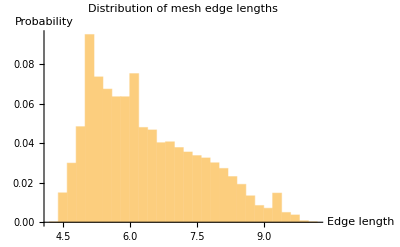

```mathematica
Sum[allEdgeLengths[[i]],{i,1,Length[allEdgeLengths]}]/Length[allEdgeLengths]
Histogram[allEdgeLengths,18,"Probability",AxesLabel->{"Edge length","Probability"},PlotLabel->"Distribution of mesh edge lengths"]
```

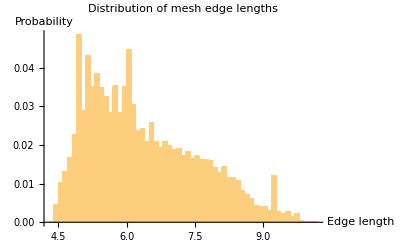

```mathematica
Histogram[allEdgeLengths,50,"Probability",AxesLabel->{"Edge length","Probability"},PlotLabel->"Distribution of mesh edge lengths"]
```

```mathematica
mu=Mean[allEdgeLengths]
sigma=StandardDeviation[allEdgeLengths]
X=77;
pCLT=CDF[NormalDistribution[10*mu,Sqrt[10]*sigma],X]
```

6.37315

1.21758

0.999716

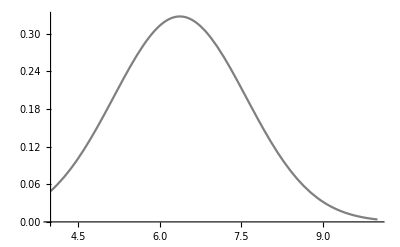

```mathematica
Plot[PDF[NormalDistribution[mu,sigma],x],{x,4,10},PlotStyle->Gray]
```

```mathematica
(*assume you already have:nodes,elements*)(*1️⃣ Compute all interior edge lengths*)edgeLengths=Table[Norm[nodes[[edge[[1]]]]-nodes[[edge[[2]]]]],{edge,elements}];

(*2️⃣ Find indices of boundary nodes*)
boundaryNodes=Flatten@Position[nodes,{x_,y_}/;x==0||x==500||y==0||y==900];

(*3️⃣ Build all edges (each triangle contributes 3)*)
allEdges=Sort/@Flatten[elements/.{a_,b_,c_}:>{{a,b},{b,c},{c,a}},1];

(*4️⃣ Select only boundary edges (both nodes on the border)*)
boundaryEdges=Select[allEdges,MemberQ[boundaryNodes,#[[1]]]&&MemberQ[boundaryNodes,#[[2]]]&];

(*5️⃣ Compute their lengths*)
boundaryEdgeLengths=Table[Norm[nodes[[e[[1]]]]-nodes[[e[[2]]]]],{e,boundaryEdges}];

(*6️⃣ Combine with interior lengths*)
allEdgeLengths=Join[edgeLengths,boundaryEdgeLengths];
```

```mathematica
matrix=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_all_points_250.csv","CSV"];Dimensions[matrix]
```

{357,7336}

```mathematica
(*Manipulate[Plot3D[ihat[[j]][x,y],{x,y}∈region,PlotRange->All],{j,1,Length[ihat],1}]*)
```

```mathematica
res=extractSeismogramFromAllNodes[matrix,83]
```

{357,4}

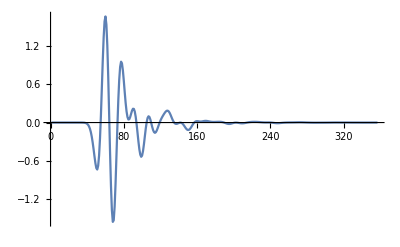

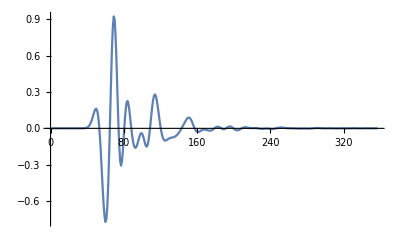

```mathematica
matrixS250=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_250.csv","CSV"];Dimensions[matrixS250]
ListLinePlot[matrixS250[[1;;-1,1]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,2]],PlotRange->All]
```

```mathematica
Norm[a-matrixS250]
```

0.

```mathematica
matrixS250=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_250.csv","CSV"];Dimensions[matrixS250]
ListLinePlot[matrixS250[[1;;-1,1]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,2]],PlotRange->All]
```

{357,4}

-Graphics-

-Graphics-

{800,4}

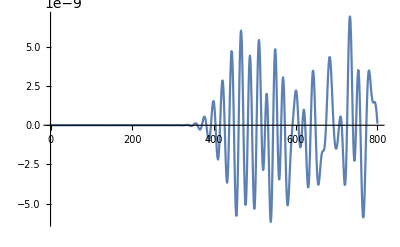

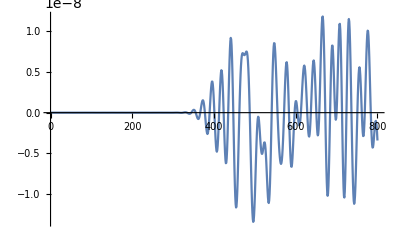

```mathematica
matrixS=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_3500.csv","CSV"];Dimensions[matrixS]
ListLinePlot[-matrixS[[1;;-1,1]],PlotRange->All]
ListLinePlot[matrixS[[1;;-1,2]],PlotRange->All]
```

```mathematica
Sum[numbers[[i]],{i,1,4*n}]
```

0

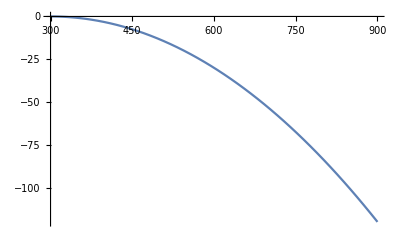

```mathematica
Plot[-(x-300)^2/3000,{x,300,900}]
```

```mathematica
(*Showing S-wave*)
```

```mathematica
calculateSourceVx[x_,y_,x0_,y0_,radius_]:=Module[{},(
dist=EuclideanDistance[{x,y},{x0,y0}];
If[dist>radius,
Return[0]];
-2*(y-y0)*Exp[-dist^2/radius^2]
)]
```

```mathematica
calculateSourceVx[nodes[[9958,1]],nodes[[9958,2]],2898.64,6106.86,300]
```

0.00688613

```mathematica
calculatePlotXY[q_,nodes_]:=Module[{n, tablex, tabley,T, timestep},(
T=Length[q];
ihat=Table[0,2,Length[q]];
n=Length[nodes];
For[j=1,j≤T,j++,
tablex = Table[{nodes[[i]],q[[j,(*2*n+*)2*i-1]]},{i,1,Length[nodes]}];
tabley = Table[{nodes[[i]],q[[j,(*2*n+*)2*i]]},{i,1,Length[nodes]}];
ihat[[1,j]] = Interpolation[tablex,InterpolationOrder->1];
ihat[[2,j]] = Interpolation[tabley,InterpolationOrder->1];
];
ihat
)]
nodes[[133]]
```

{41.,50.}

```mathematica
elements[[19666]]
```

{9958,10118,10227}

```mathematica
sWave004=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_1.csv","CSV"];
```

0.040426

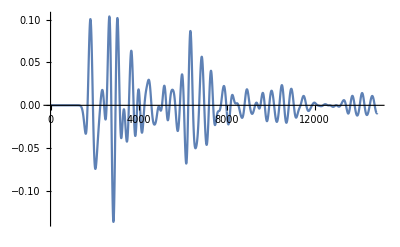

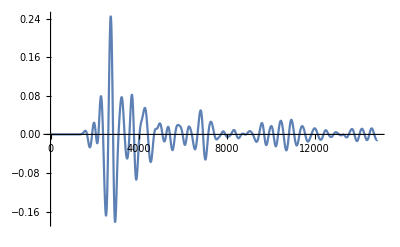

```mathematica
0.040426
ListLinePlot[sWave004[[1;;-1,1]],PlotRange->All]
ListLinePlot[sWave004[[1;;-1,2]],PlotRange->All]
```

```mathematica
Dimensions[sWave]
```

{22266,4}

```mathematica
sWave014=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_1.csv","CSV"];
```

0.140426

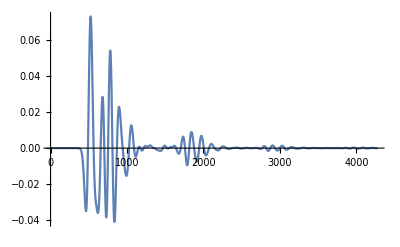

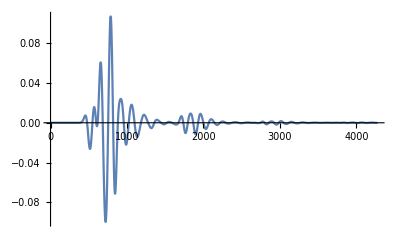

```mathematica
0.140426
ListLinePlot[sWave014[[1;;-1,1]],PlotRange->All]
ListLinePlot[sWave014[[1;;-1,2]],PlotRange->All]
```

0.351065

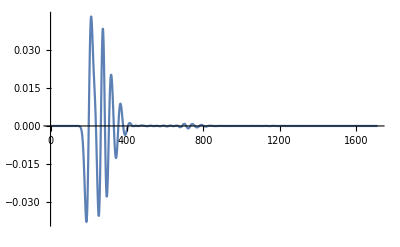

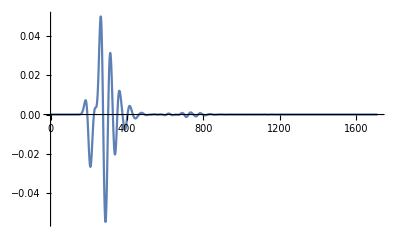

```mathematica
0.351065
sWave035=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_1.csv","CSV"];
ListLinePlot[sWave035[[1;;-1,1]],PlotRange->All]
ListLinePlot[sWave035[[1;;-1,2]],PlotRange->All]
```

0.1

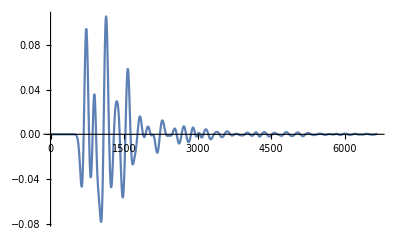

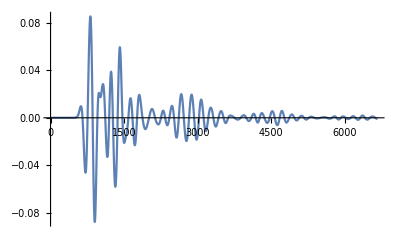

```mathematica
0.1
sWave01=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_1.csv","CSV"];
ListLinePlot[sWave01[[1;;-1,1]],PlotRange->All]
ListLinePlot[sWave01[[1;;-1,2]],PlotRange->All]
```

```mathematica
EuclideanDistance[nodes[[95]],{170,17}]
```

151.634

```mathematica
ArcSin[150/151.63442880823618]/Pi*180
```

81.58

```mathematica
111.19*1.5
```

166.785

{59.,50.}

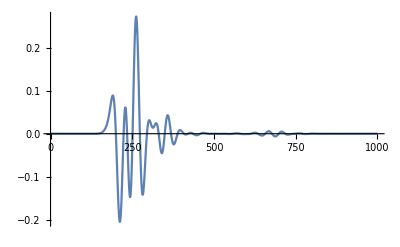

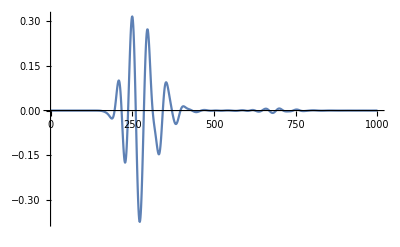

```mathematica
nodes[[169]]
```

```mathematica
sWave3d=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_1.csv","CSV"];
```

```mathematica
Dimensions[sWave3d]
```

{4,32452}

```mathematica
ihat=Table[0,Length[sWave3d],2];
n=Length[nodes];
```

```mathematica
For[j=1,j≤4,j++,
tablex = Table[{nodes[[i]],sWave3d[[j,2*i-1]]},{i,1,Length[nodes]}];
tabley = Table[{nodes[[i]],sWave3d[[j,2*i]]},{i,1,Length[nodes]}];
ihat[[j,1]] = Interpolation[tablex,InterpolationOrder->1];
ihat[[j,2]] = Interpolation[tabley,InterpolationOrder->1];
];
```

```mathematica
ihat
```

{{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
calculatePlotXY[sWave3d, nodes];
```

```mathematica
(*Manipulate[Plot3D[ihat[[1,j]][x,y],{x,y}∈region,PlotRange->All],{j,1,Length[ihat],1}]*)
```

```mathematica
(*Manipulate[Plot3D[ihat[[2,j]][x,y],{x,y}∈region,PlotRange->All],{j,1,Length[ihat],1}]*)
```

```mathematica
smallerRegion= Rectangle[{200,200},{9800,9800}];
```

```mathematica
divergence=Derivative[1,0][ihat[[1,1]]][x,y]+Derivative[0,1][ihat[[2,1]]][x,y];
```

```mathematica
Plot3D[divergence,{x,y}∈smallerRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
curl = Derivative[0,1][ihat[[1,1]]][x,y]-Derivative[1,0][ihat[[2,1]]][x,y];
```

```mathematica
Plot3D[curl,{x,y}∈smallerRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
matrixS250M=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\MFEM_seismogram_displ_vel_5000.csv"];
```

```mathematica
Norm[matrixS250E-matrixS250]/Norm[matrixS250]
```

0.0000894866

```mathematica
(*lambda1e7mu1e9=matrixS250;*)
```

```mathematica
(*lambda1e9mu1e7=matrixS250;*)
```

```mathematica
Norm[matrixS250]
Norm[ lambda1e9mu1e7]
```

3360.26

22219.4

{608,48}

400

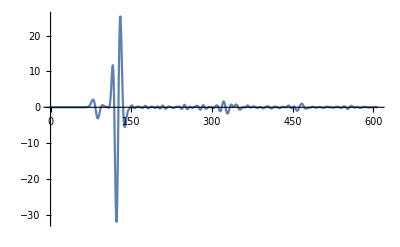

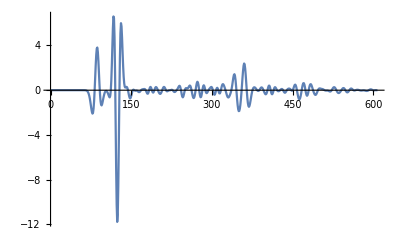

```mathematica
matrixS250=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displ_vel_5000.csv"];Dimensions[matrixS250]

400
ListLinePlot[matrixS250[[1;;-1,1]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,2]],PlotRange->All]
```

```mathematica
pvel=Sqrt[(27/4*10^9*0+2*27/8*10^9)/600.]
```

3354.1

```mathematica
nodes[[150]]
```

{281.69,0.}

```mathematica
dist=EuclideanDistance[{2898.64,6106.86},{281.69,0}]
```

6643.96

```mathematica
dist/pvel
```

1.98085

```mathematica
100*tau
```

2.48332

1000

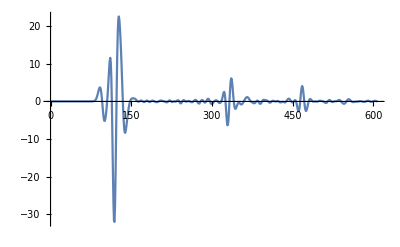

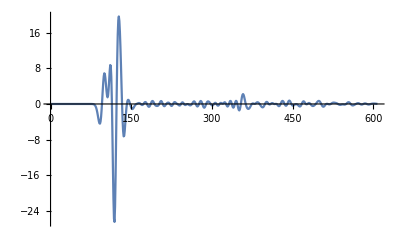

```mathematica
1000
ListLinePlot[matrixS250[[1;;-1,5]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,6]],PlotRange->All]
```

2000

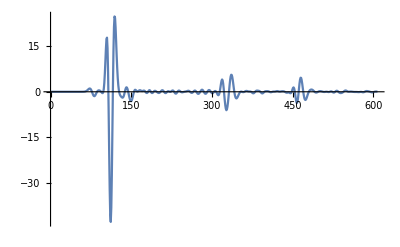

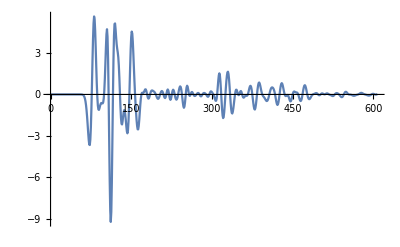

```mathematica
2000
ListLinePlot[matrixS250[[1;;-1,9]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,10]],PlotRange->All]
```

3000

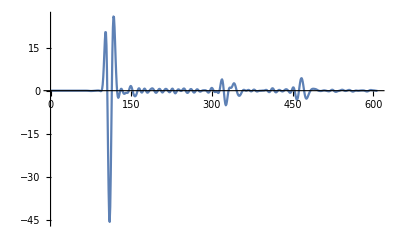

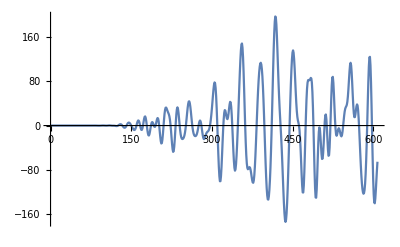

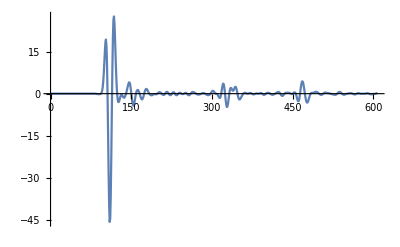

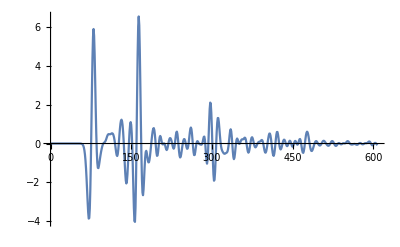

```mathematica
3000
ListLinePlot[matrixS250[[1;;-1,13]],PlotRange->All]
ListLinePlot[lambda1e9mu1e7[[1;;-1,13]],PlotRange->All]
ListLinePlot[lambda1e7mu1e9[[1;;-1,13]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,14]],PlotRange->All]
```

4000

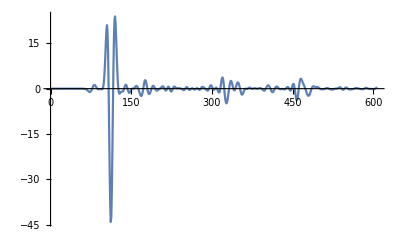

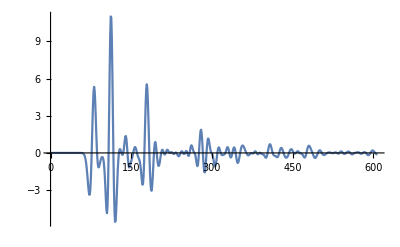

```mathematica
4000
ListLinePlot[matrixS250[[1;;-1,17]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,18]],PlotRange->All]
```

5000

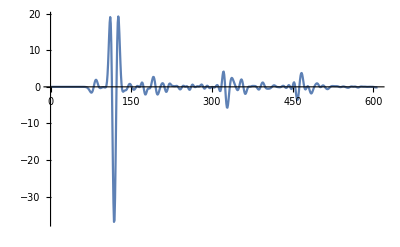

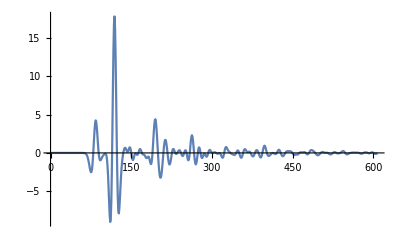

```mathematica
5000
ListLinePlot[matrixS250[[1;;-1,21]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,22]],PlotRange->All]
```

6000

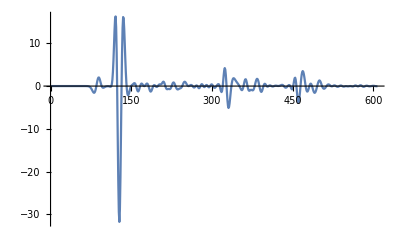

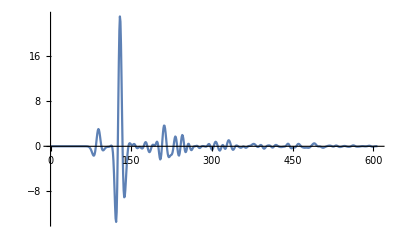

```mathematica
6000
ListLinePlot[matrixS250[[1;;-1,25]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,26]],PlotRange->All]
```

7000

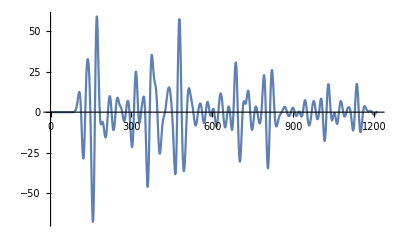

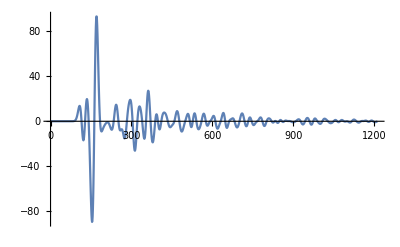

```mathematica
7000
ListLinePlot[matrixS250[[1;;-1,29]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,30]],PlotRange->All]
```

8000

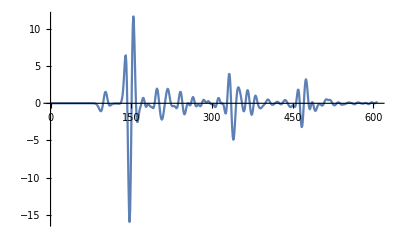

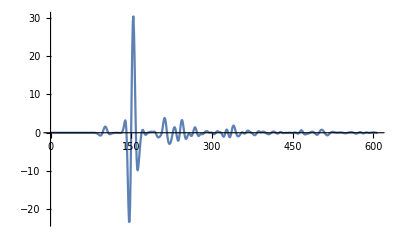

```mathematica
8000
ListLinePlot[matrixS250[[1;;-1,33]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,34]],PlotRange->All]
```

9000

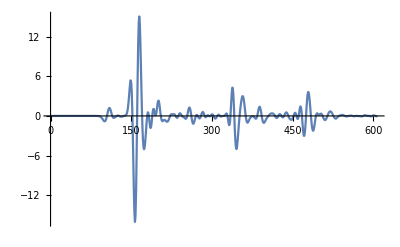

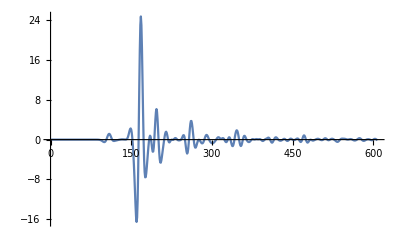

```mathematica
9000
ListLinePlot[matrixS250[[1;;-1,37]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,38]],PlotRange->All]
```

200

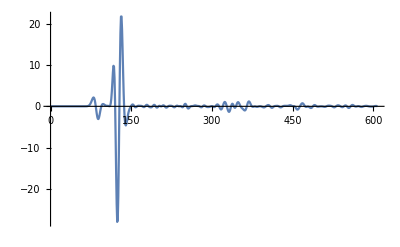

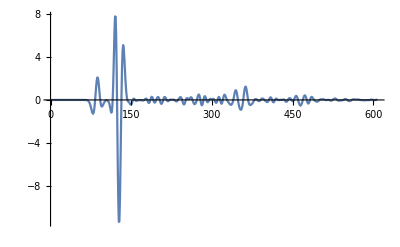

```mathematica
200
ListLinePlot[matrixS250[[1;;-1,41]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,42]],PlotRange->All]
```

9800

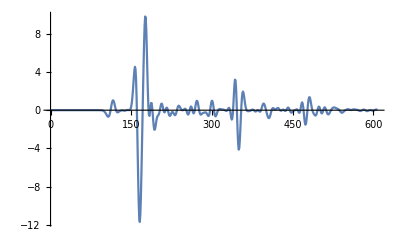

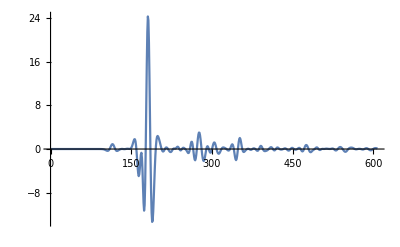

```mathematica
9800
ListLinePlot[matrixS250[[1;;-1,45]],PlotRange->All]
ListLinePlot[matrixS250[[1;;-1,46]],PlotRange->All]
```

```mathematica
elements[[19666]]
sEl=nodes[[elements[[19666]]]]
```

{9958,10118,10227}

{{2898.64,6106.86},{2921.49,6014.87},{3002.13,6083.74}}

```mathematica
Total[sEl]/3
```

{2940.75,6068.49}

```mathematica
(* sources for v_x and v_y*)
vx=LinearSolve[{Flatten[{1,sEl[[1]]}],Flatten[{1,sEl[[2]]}],Flatten[{1,sEl[[3]]}]},{7000*A,0,-A}]
```

{-220891. A,-53.6264 A,62.7712 A}

```mathematica
vy=LinearSolve[{Flatten[{1,sEl[[1]]}],Flatten[{1,sEl[[2]]}],Flatten[{1,sEl[[3]]}]},{0,A,-70*A}]
```

{3240.27 A,-0.718699 A,-0.189462 A}

```mathematica
(*vx/dy-vy/dx*)
vx[[3]]-vy[[2]]
```

63.4899 A

```mathematica
N[Sqrt[27/8*10^9/900]]
N[Sqrt[27/8*10^9/300]]
```

1936.49

3354.1

```mathematica
Flatten[{1,sEl[[1]]}]
```

{1,2898.64,6106.86}

```mathematica
vp=EuclideanDistance[{400,upper},{3000.,6000}]/(0.0248332*45);
vs=0.5*vp
```

2134.57

```mathematica
vs/6
```

355.762

{1469,14}

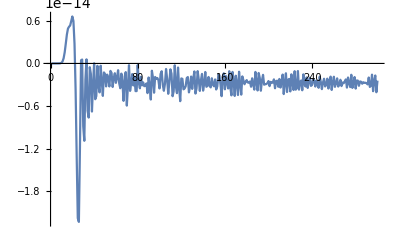

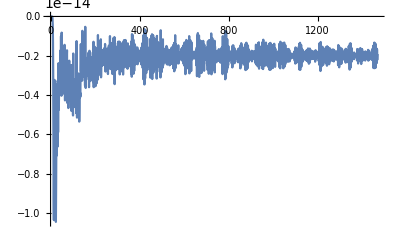

```mathematica
(*Before ricker wavelet*)
matrixS=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displacement_15.csv","CSV"];Dimensions[matrixS]
ListLinePlot[matrixS[[1;;300,5]],PlotRange->All]
ListLinePlot[matrixS[[1;;-1,6]],PlotRange->All]
```

{1469,14}

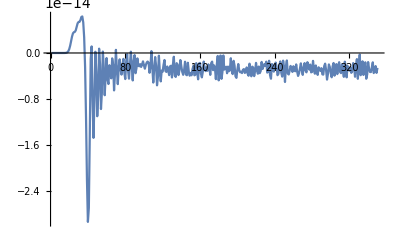

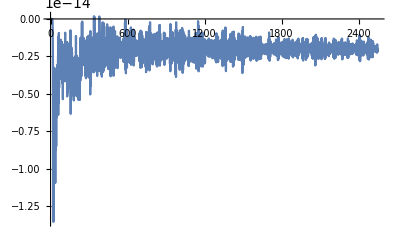

```mathematica
matrixS5=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displacement_5.csv","CSV"];Dimensions[matrixS]
ListLinePlot[matrixS5[[1;;350,5]],PlotRange->All]
ListLinePlot[matrixS5[[1;;-1,6]],PlotRange->All]
```

```mathematica
ricker[t_,f0_]:=Module[{a,tshift},(
tshift=1./f0;
a=Pi*f0*(t-tshift);
(1-2*a^2)*Exp[-a^2]
)]
```

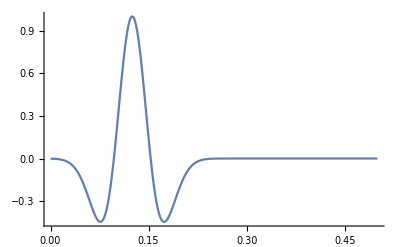

```mathematica
Plot[ricker[t,8],{t,0,0.5},PlotRange->All]
```

```mathematica
Integrate[ricker[t,8],{t,0,0.28}]
```

6.50518×10^-6

```mathematica
rckr=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\ricker","CSV"];
```

```mathematica
Dimensions[rckr]
```

{1,163}

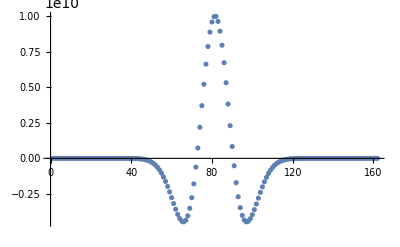

```mathematica
ListPlot[rckr[[1,1;;163]], PlotRange->All]
```

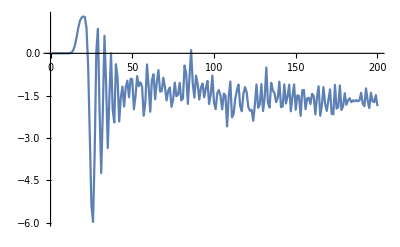

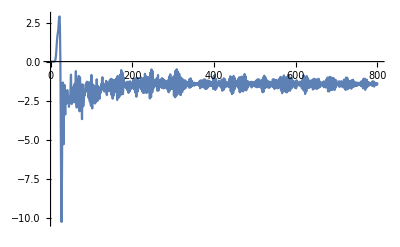

```mathematica
ListLinePlot[matrixS[[1;;200,3]],PlotRange->All]
ListLinePlot[matrixS[[1;;800,4]],PlotRange->All]
```

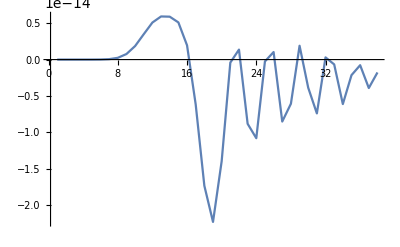

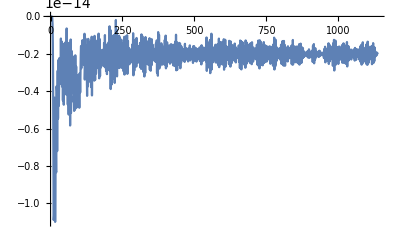

```mathematica
matrixS=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displacement_25.csv","CSV"];ListLinePlot[matrixS[[1;;38,5]],PlotRange->All]
ListLinePlot[matrixS[[1;;-1,6]],PlotRange->All]
```

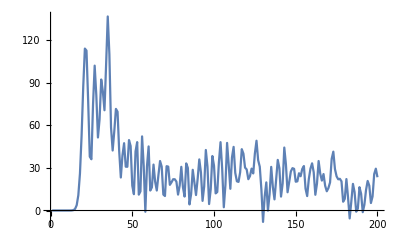

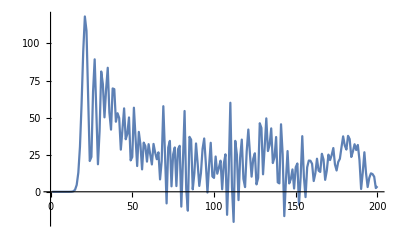

```mathematica
ListLinePlot[matrixS[[1;;200,7]],PlotRange->All]
ListLinePlot[matrixS[[1;;200,8]],PlotRange->All]
```

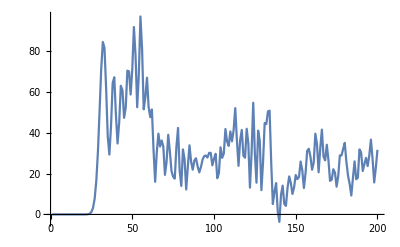

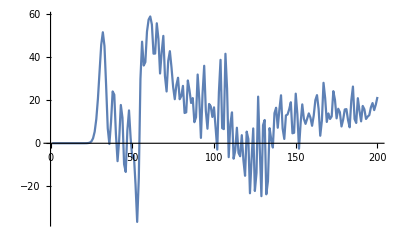

```mathematica
ListLinePlot[matrixS[[1;;200,9]],PlotRange->All]
ListLinePlot[matrixS[[1;;200,10]],PlotRange->All]
```

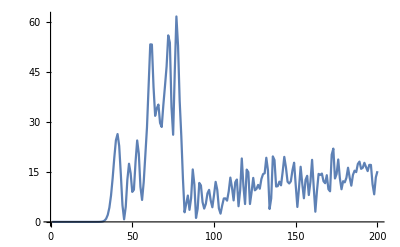

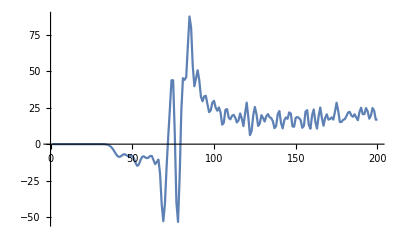

```mathematica
ListLinePlot[matrixS[[1;;200,11]],PlotRange->All]
ListLinePlot[matrixS[[1;;200,12]],PlotRange->All]
```

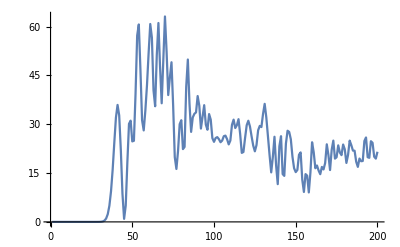

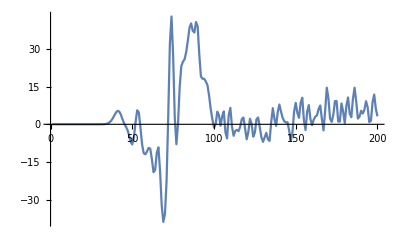

```mathematica
ListLinePlot[matrixS[[1;;200,13]],PlotRange->All]
ListLinePlot[matrixS[[1;;200,14]],PlotRange->All]
```

```mathematica
Sum[nodes[[elements[[6242,i]]]],{i,1,3}]/3
```

{307.472,199.004}

```mathematica
EuclideanDistance[Sum[nodes[[elements[[6242,i]]]],{i,1,3}]/3,nodes[[1033]]]
```

274.459

```mathematica
nodes[[137]]
```

{190.,300.}

{72730,2}

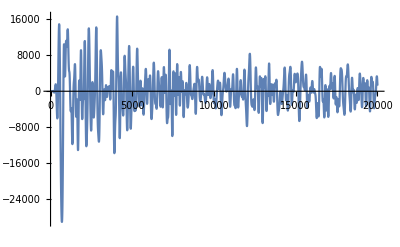

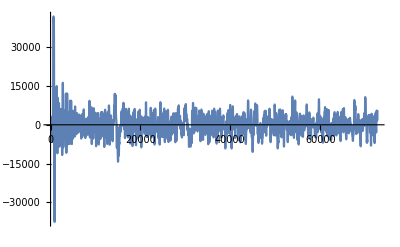

```mathematica
matrixS=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_displacement_250000.csv","CSV"];Dimensions[matrixS]
ListLinePlot[matrixS[[1;;20000,1]],PlotRange->All]
ListLinePlot[matrixS[[All,2]],PlotRange->All]
```

{567,2}

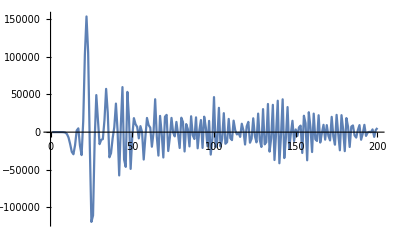

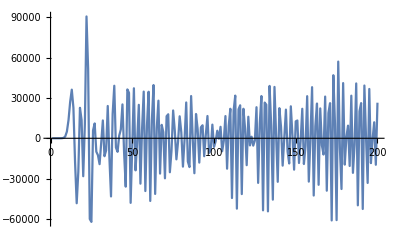

```mathematica
matrixSV=Import["C:\\Users\\Petar\\source\\repos\\FEM2D\\MFEM_all_solutions_seismograph_points.csv","CSV"];Dimensions[matrixSV]
ListLinePlot[matrixSV[[1;;200,1]],PlotRange->All]
ListLinePlot[matrixSV[[1;;200,2]],PlotRange->All]
```

```mathematica
zyy
```

```mathematica
mfemnorm=Norm[matrixMFEM[[60]]]
eigennorm=Norm[matrix[[60]]]
Norm[matrix[[60]]-matrixMFEM[[60]]]
```

137.829

137.877

0.259223

```mathematica
Dimensions[ihat]
```

{1702}

```mathematica
matrixMFEM=Import["C:\\Users\\Petar\\source\\repos\\FEM2D\\MFEM_all_solutions.csv","CSV"];
```

Import::nffil: File C:\Users\Petar\source\repos\FEM2D\MFEM_all_solutions.csv not found during Import.

```mathematica
(*------------------TESTING------------------*)
```

```mathematica
(*Case for only lambda difference in a few elements, maxCellMeasure=50*)
nodes[[elements[[180]]]]
ϕ={{(x+300)/6.977},{1.-(x+300)/6.977+(y-500)/7.042},{(500-y)/7.042}}
```

{{-293.023,500.},{-300.,500.},{-300.,492.958}}

{{0.143328 (300+x)},{1.-0.143328 (300+x)+0.142005 (-500+y)},{0.142005 (500-y)}}

```mathematica
ϕ/.x->-293.023/.y->500
```

{{1.},{3.44169×10^-15},{0.}}

```mathematica
divshape={Flatten[{D[ϕ,x],D[ϕ,y]}]}
```

{{0.143328,-0.143328,0,0,0.142005,-0.142005}}

```mathematica
Transpose[divshape].divshape
```

{{0.0205429,-0.0205429,0.,0.,0.0203533,-0.0203533},{-0.0205429,0.0205429,0.,0.,-0.0203533,0.0203533},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.0203533,-0.0203533,0.,0.,0.0201655,-0.0201655},{-0.0203533,0.0203533,0.,0.,-0.0201655,0.0201655}}

```mathematica
elements[[180]]
```

{74,72,71}

```mathematica
elements[[1]]
```

{309,77,79}

```mathematica
1/6.977
```

0.143328

```mathematica
Φ={{1-ξ-η,0,ξ,0,η,0},{0,1-ξ-η,0,ξ,0,η}}
```

{{1-η-ξ,0,ξ,0,η,0},{0,1-η-ξ,0,ξ,0,η}}

```mathematica
localM0=Integrate[Φ,{ξ,0,1},{η,0,1-ξ}]
```

{{1/6,0,1/6,0,1/6,0},{0,1/6,0,1/6,0,1/6}}

```mathematica
dots=nodes[[elements[[2]]]]
```

{{-300.,7.04225},{-300.,0.},{-293.023,0.}}

```mathematica
Sum[dots[[All,1]][[i]]/3,{i,1,3}]
```

-297.674

```mathematica
localM0=Integrate[Transpose[Φ].Φ,{ξ,0,1},{η,0,1-ξ}]
```

{{1/12,0,1/24,0,1/24,0},{0,1/12,0,1/24,0,1/24},{1/24,0,1/12,0,1/24,0},{0,1/24,0,1/12,0,1/24},{1/24,0,1/24,0,1/12,0},{0,1/24,0,1/24,0,1/12}}

```mathematica
N[localM0]
```

{{0.0833333,0.,0.0416667,0.,0.0416667,0.},{0.,0.0833333,0.,0.0416667,0.,0.0416667},{0.0416667,0.,0.0833333,0.,0.0416667,0.},{0.,0.0416667,0.,0.0833333,0.,0.0416667},{0.0416667,0.,0.0416667,0.,0.0833333,0.},{0.,0.0416667,0.,0.0416667,0.,0.0833333}}

```mathematica
d={{2*μ+λ,λ,0},{λ,2*μ+λ,0},{0,0,μ}};
basisFunctions={1-ξ-η,ξ,η};
```

```mathematica
bFξ=D[basisFunctions,ξ];
bFη=D[basisFunctions,η];
```

```mathematica
(*Case for higher order elements*)
B={{bFξ[[1]],bFη[[1]],0,0,0,0,bFξ[[2]],bFη[[2]],0,0,0,0,bFξ[[3]],bFη[[3]],0,0,0,0},
{0,0,bFξ[[1]],bFη[[1]],0,0,0,0,bFξ[[2]],bFη[[2]],0,0,0,0,bFξ[[3]],bFη[[3]],0,0},
{0,0,0,0,bFξ[[1]],bFη[[1]],0,0,0,0,bFξ[[2]],bFη[[2]],0,0,0,0,bFξ[[3]],bFη[[3]]}}
```

{{-1,-1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,-1,-1,0,0,0,0,1,0,0,0,0,0,0,1,0,0},{0,0,0,0,-1,-1,0,0,0,0,1,0,0,0,0,0,0,1}}

```mathematica
Transpose[B].d.B
```

{{λ+2 μ,λ+2 μ,λ,λ,0,0,-λ-2 μ,0,-λ,0,0,0,0,-λ-2 μ,0,-λ,0,0},{λ+2 μ,λ+2 μ,λ,λ,0,0,-λ-2 μ,0,-λ,0,0,0,0,-λ-2 μ,0,-λ,0,0},{λ,λ,λ+2 μ,λ+2 μ,0,0,-λ,0,-λ-2 μ,0,0,0,0,-λ,0,-λ-2 μ,0,0},{λ,λ,λ+2 μ,λ+2 μ,0,0,-λ,0,-λ-2 μ,0,0,0,0,-λ,0,-λ-2 μ,0,0},{0,0,0,0,μ,μ,0,0,0,0,-μ,0,0,0,0,0,0,-μ},{0,0,0,0,μ,μ,0,0,0,0,-μ,0,0,0,0,0,0,-μ},{-λ-2 μ,-λ-2 μ,-λ,-λ,0,0,λ+2 μ,0,λ,0,0,0,0,λ+2 μ,0,λ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-λ,-λ,-λ-2 μ,-λ-2 μ,0,0,λ,0,λ+2 μ,0,0,0,0,λ,0,λ+2 μ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-μ,-μ,0,0,0,0,μ,0,0,0,0,0,0,μ},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-λ-2 μ,-λ-2 μ,-λ,-λ,0,0,λ+2 μ,0,λ,0,0,0,0,λ+2 μ,0,λ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-λ,-λ,-λ-2 μ,-λ-2 μ,0,0,λ,0,λ+2 μ,0,0,0,0,λ,0,λ+2 μ,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-μ,-μ,0,0,0,0,μ,0,0,0,0,0,0,μ}}

```mathematica
protoM1={{bFξ[[1]],0,bFξ[[2]],0,bFξ[[3]],0},
{bFη[[1]],0,bFη[[2]],0,bFη[[3]],0},
{0,bFξ[[1]],0,bFξ[[2]],0,bFξ[[3]]},
{0,bFη[[1]],0,bFη[[2]],0,bFη[[3]]}
}
```

{{-1,0,1,0,0,0},{-1,0,0,0,1,0},{0,-1,0,1,0,0},{0,-1,0,0,0,1}}

```mathematica
(*Test matrix multiplication for calculation of M1*)
{{df1/dxi,df1/deta,0,0,0,0,df2/dxi,df2/deta,0,0,0,0,df3/dxi,df3/deta,0,0,0,0},
{0,0,df1/dxi,df1/deta,0,0,0,0,df2/dxi,df2/deta,0,0,0,0,df3/dxi,df3/deta,0,0},
{0,0,0,0,df1/dxi,df1/deta,0,0,0,0,df2/dxi,df2/deta,0,0,0,0,df3/dxi,df3/deta}}.
{{dxi/dx,0,0,0,0,0},
{deta/dx,0,0,0,0,0},
{0,dxi/dy,0,0,0,0},
{0,deta/dy,0,0,0,0},
{dxi/dy,dxi/dx,0,0,0,0},
{deta/dy,deta/dx,0,0,0,0},
{0,0,dxi/dx,0,0,0},
{0,0,deta/dx,0,0,0},
{0,0,0,dxi/dy,0,0},
{0,0,0,deta/dy,0,0},
{0,0,dxi/dy,dxi/dx,0,0},
{0,0,deta/dy,deta/dx,0,0},
{0,0,0,0,dxi/dx,0},
{0,0,0,0,deta/dx,0},
{0,0,0,0,0,dxi/dy},
{0,0,0,0,0,deta/dy},
{0,0,0,0,dxi/dy,dxi/dx},
{0,0,0,0,deta/dy,deta/dx}
}/2
```

{{df1/dx,0,df2/dx,0,df3/dx,0},{0,df1/dy,0,df2/dy,0,df3/dy},{df1/dy,df1/dx,df2/dy,df2/dx,df3/dy,df3/dx}}

```mathematica
Dd={{1,0.5,0},
{0.5,1,0},
{0,0,0.25}};
Integrate[Transpose[B].Dd.B*150000,{x,0,1},{y,0,1-x}]
dots=nodes[[elements[[1]]]]
```

```mathematica
xxx={{0,1./500},{-1./300,-1./500},{1./300,0}};
Div[xxx,{x,y}]
```

{0,0,0}

```mathematica
vvv={1,2,3};
Grad[vvv,{x,y}]
```

{{0,0},{0,0},{0,0}}

```mathematica
(*Debugging MFEM approach*)
dofs={{y/500},{1-(x+300)/300-y/500},{(x+300)/300}}
dofs/.{x->-300,y->0}
dofs/.{x->-300,y->500}
dofs/.{x->0,y->0}
```

{{y/500},{1+1/300 (-300-x)-y/500},{(300+x)/300}}

{{0},{1},{0}}

{{1},{0},{0}}

{{0},{0},{1}}

```mathematica
λ=0.5;
Λ=Table[If[i<=3,D[dofs[[i]],x],D[dofs[[i-3]],y]],{i,1,6}]

λ*Integrate[Λ.Transpose[Λ],{x,-300,0},{y,0,(x+300)/300*500}]
```

{{0},{-1/300},{1/300},{1/500},{-1/500},{0}}

{{0.,0.,0.,0.,0.,0.},{0.,0.416667,-0.416667,-0.25,0.25,0.},{0.,-0.416667,0.416667,0.25,-0.25,0.},{0.,-0.25,0.25,0.15,-0.15,0.},{0.,0.25,-0.25,-0.15,0.15,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
Grad[dofs,{x,y}]
```

{{{0,1/500}},{{-1/300,-1/500}},{{1/300,0}}}

```mathematica
gshape=Transpose[{Flatten[D[dofs,x]],Flatten[D[dofs,y]]}]
divshape=Flatten[{Transpose[gshape][[1]],Transpose[gshape][[2]]}]
elmatλ=Table[divshape[[i]]*divshape[[j]],{i,1,6},{j,1,6}]
elmatμ = Table[0,6,6];
For[ii=1,ii≤2,ii++,
For[jj=1,jj≤2,jj++,
For[kk=1,kk≤3,kk++,
For[ll=1,ll≤3,ll++,
elmatμ[[3*ii+kk-3,3*jj+ll-3]]=gshape[[kk,jj]]*gshape[[ll,ii]]
]
]
]
]
elmatμ
```

{{0,1/500},{-1/300,-1/500},{1/300,0}}

{0,-1/300,1/300,1/500,-1/500,0}

{{0,0,0,0,0,0},{0,1/90000,-1/90000,-1/150000,1/150000,0},{0,-1/90000,1/90000,1/150000,-1/150000,0},{0,-1/150000,1/150000,1/250000,-1/250000,0},{0,1/150000,-1/150000,-1/250000,1/250000,0},{0,0,0,0,0,0}}

{{0,0,0,0,-1/150000,1/150000},{0,1/90000,-1/90000,0,1/150000,-1/150000},{0,-1/90000,1/90000,0,0,0},{0,0,0,1/250000,-1/250000,0},{-1/150000,1/150000,0,-1/250000,1/250000,0},{1/150000,-1/150000,0,0,0,0}}

```mathematica
gshape[[1,2]]*gshape[[2,1]]
```

-1/150000

```mathematica
(*razgledai M1 kak se stroeshe*)
(*Double check with:
dofs={1-x-y,x,y}*)
B={{D[dofs[[1]],x][[1]],0,D[dofs[[2]],x][[1]],0,D[dofs[[3]],x][[1]],0},
{0,D[dofs[[1]],y][[1]],0,D[dofs[[2]],y][[1]],0,D[dofs[[3]],y][[1]]},
{D[dofs[[1]],y][[1]],D[dofs[[1]],x][[1]],D[dofs[[2]],y][[1]],D[dofs[[2]],x][[1]],D[dofs[[3]],y][[1]],D[dofs[[3]],x][[1]]}
}
```